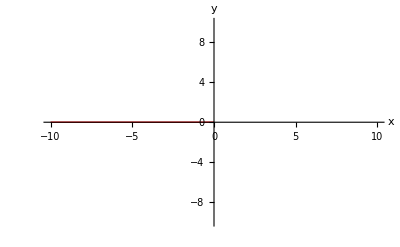

```mathematica
Plot[0,{x,-10,0},PlotRange->{{-10,10},{-10,10}}, PlotStyle->{Red,Thick},AxesLabel->{x,y}]
```

```mathematica
ParametricPlot3D[{x,0,z},{x,-10,0},{z,-100,100},PlotRange->{{-10,10},{-10,10},{-20,20}}, PlotStyle->{Red,Thick}]
```

-Graphics3D-

```mathematica
BLeq[ψ_, m_]= With[{u = D[ψ[x,y],y],v = -D[ψ[x,y],x], U =A(- x)^(1/2-m)},u D[u,x] + v D[u,y]- U D[U,x]-ν D[u,{y,2}]]
```

A^2 (1/2-m) (-x)^(-2 m)-ν ψ^(0,3)[x,y]-ψ^(0,2)[x,y] ψ^(1,0)[x,y]+ψ^(0,1)[x,y] ψ^(1,1)[x,y]

```mathematica
A=1
```

1

```mathematica
Ψ[x_,y_] := Sqrt[ν ] (-x)^(3/4-m/2) f[y/(Sqrt[ν] (-x)^(m/2+1/4))];
```

```mathematica
Eq[m_, f_]:=Evaluate[FullSimplify[4 (-x)^(2 m)BLeq[Ψ,m]/.{ y->(-x)^(m/2+1/4)z Sqrt[ν]}]]
```

```mathematica
sol0f[L_]:= f[z]/.NDSolve[{Eq[0,f]==0,f[1]==1/12,f'[1]==1/4, f''[1]==1/2},f,{z,1,L},
Method->{"Adams"}][[1]]
```

```mathematica
f0 = sol0f[6.7]
```

InterpolatingFunction[…][z]

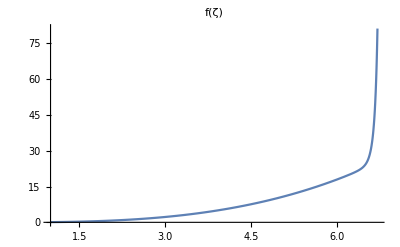

```mathematica
Plot[f0,{z,1,6.7},PlotRange->All, PlotLabel->f[ζ]]
```

```mathematica
f1 = f[z]/.NDSolve[{Eq[0,f]==0,f[2]==2-4/3,f'[2]==1, f''[2]==0},f,{z,2,6.7},
Method->{"Adams"}][[1]]
```

InterpolatingFunction[…][z]

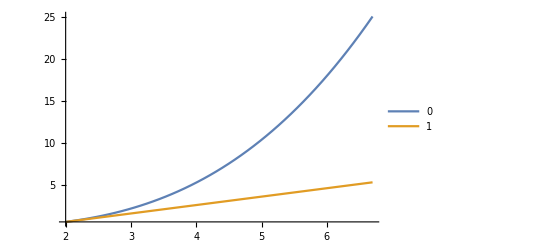

```mathematica
Plot[{z^3/12,f1},{z,2,6.7},PlotRange->All, PlotLegends->{0,1}]
```

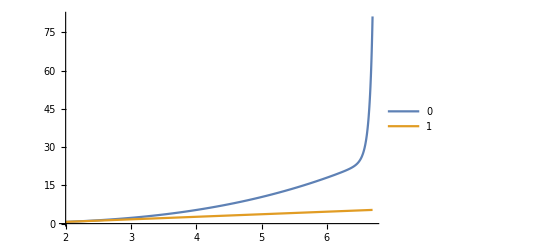

```mathematica
Plot[{f0,f1},{z,2,6.7},PlotRange->All, PlotLegends->{0,1}]
```

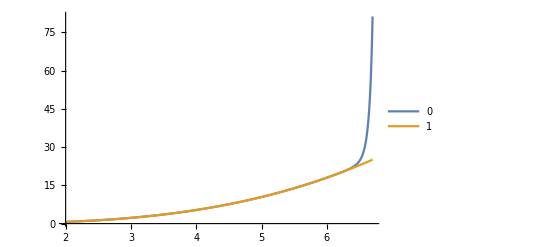

```mathematica
Plot[{f0,z^3/12},{z,2,6.7},PlotRange->All, PlotLegends->{0,1}]
```

```mathematica
f2= f[z]/.NDSolve[{Eq[0,f]==0,f[2]==2-4/3,f'[2]==1, f''[2]==0},f,{z,2,15},
Method->{"Adams"}][[1]]
```

InterpolatingFunction[…][z]

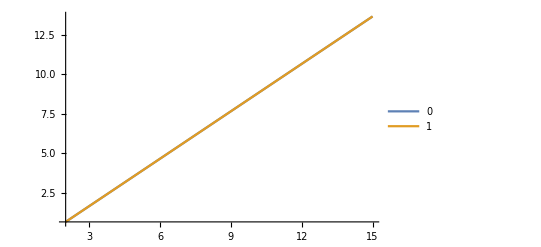

```mathematica
Plot[{f1,f2},{z,2,15},PlotRange->All, PlotLegends->{0,1}]
```

```mathematica
f[t_] := t^3/12;
```

```mathematica
Eq[0, f]
```

0

```mathematica
eqal=Simplify[((-2+4 m) f'[z]^2+(3-2 m) f[z] f''[z])/.{f'[z]-> α z^(α-1),f''[z]->α(α-1) z^(α-2),f[z]->z^α}]/.z->1
```

α (-3+α+2 m (1+α))

```mathematica
sola[m_]=α/.Evaluate[Solve[eqal==0,α][[2]]]
```

(3-2 m)/(1+2 m)

```mathematica
Eq[0,f]
```

{-ν s^(3)[z],0,0}[0,f]

```mathematica
Eqp[p_,u_] :=Evaluate[Simplify[Eq[0,f]/.{f'[z]->p[u], f''[z]-> p[u] p'[u], D[f[z],{z,3}]-> p'[u]^2 p[u] + p''[u] p[u]^2, f[z]->u}]]
```

```mathematica
Eqp[p,u]
```

2+p[u] (3 u-4 p'[u]) p'[u]-2 p[u]^2 (1+2 p''[u])

```mathematica
Solp[L_, p0_]:= p/.NDSolve[{Eqp[p,u]==0,p[0]==p0,p[L]==1},p,{u,0,L},Method->{"Adams"(*, "StartingInitialConditions"->{p[0]==p0}*)}][[1]]
```

```mathematica
p0=Solp[29,0.409]
```

InterpolatingFunction[…]

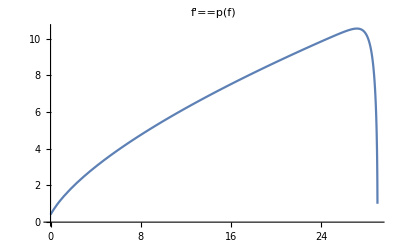

```mathematica
Plot[p0[u],{u,0,29},PlotLabel->f'==p[f]]
```

```mathematica
zsol = z/.NDSolve[{z'[f]==1/p0[f],z[0]==0},z,{f,0,29}][[1]]
```

InterpolatingFunction[…]

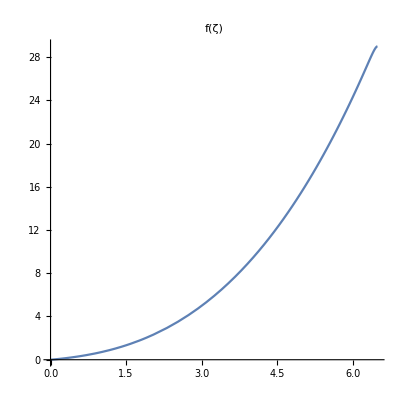

```mathematica
ParametricPlot[{zsol[f],f},{f,0,29},AspectRatio->1,PlotLabel->f[ζ]]
```

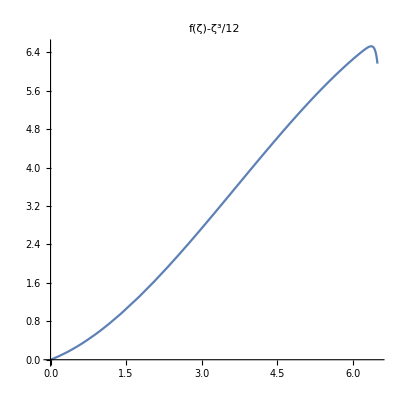

```mathematica
ParametricPlot[{zsol[f],f - zsol[f]^3/12},{f,0,29},AspectRatio->1,PlotLabel->f[ζ] - ζ^3/12]
```

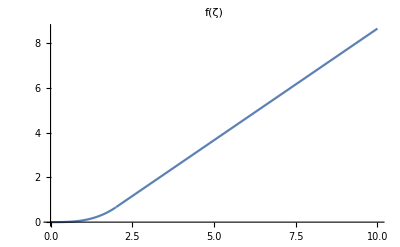

```mathematica
Plot[If[z<2,z^3/12,z-4/3],{z,0,10},PlotLabel->f[ζ]]
```